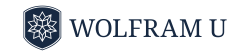

# Introduction to Quantum Computing

## Lesson 2: Quantum Circuits and Qubits

## Overview

Now we’ll dive directly into quantum computation. We’ll introduce common terms and concepts widely used in quantum information. Some details will be only briefly mentioned in this chapter. For each topic, we’ll highlight what to focus on for a first exposure, and later we’ll return to expand on each concept in more depth.

## Quantum Circuits and Qubits

In quantum computing, information is encoded in quantum states, which we transform into new states through some operations (i.e., quantum gates) tailored to a computational goal. Both states and transformations (i.e. their gates) have useful visual representations. In this chapter, we will emphasize visual intuition first and introduce the detailed mathematics later.

Since we will use the Wolfram Quantum Framework, we first need to install it.

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]

The diagram below represents an example of a quantum circuit:

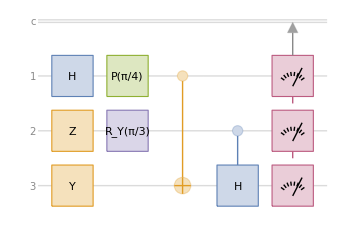

```mathematica
qc=QuantumCircuitOperator[{"H","Z"->2,"Y"->3,"P"[π/4],"CNOT"->{1,3},"RY"[π/3]->2,"CH"->{2,3},Range[3]}];
qc["Diagram"]
```

A quantum circuit is read from left to right. Looking into a quantum circuit, pay attention to wires, boxes, and how they are connected. The first operation, represented by the blue box labeled H, acts only on the first wire, while some operations act on more than one wire; they are multi-qubit gates. The boxes that look like gauges on the right hand side of the diagram represent measurement and point to the wire labeled c. The wire labeled c represents a classical system (such as part of a regular computer) where the results of the measurements on qubits are stored.  All operations shown except for measurements are unitary and reversible, a key feature we’ll explore in more detail later. You can think of each box as performing a transformation on the quantum state of one or more wires. These transformations must obey fundamental principles dictated by quantum theory.

Notice how the circuit diagram has several wires, labeled c, 1, 2 and 3. Wires 1, 2 and 3 represent qubits (quantum bits) instead of classical bits. They carry quantum data. The above circuit is a 3-qubit system, meaning that the state can be described in the complex vector space ℂ^8. There are 8 possible bitstrings for 3 classical bits.

```mathematica
StringJoin/@Tuples[{"0","1"},3]
```

{000,001,010,011,100,101,110,111}

## Quantum Basis and State

These eight classical bits can form a convenient basis (usually called as the computational basis) for the complex vector space ℂ^8. Although the notation looks very similar to the classical one, but those 3-bits in quantum are represented by wrapping them around a notation … which is called a ket. In general, a ket is a shorthand representation of a complex-valued vector, although a ket with n-bitstring represents a n-dimensional unit vector. A general 3-qubit state is a complex linear combination of those eight basis states.

Show the vectors corresponding to computational basis of 3-qubits:

```mathematica
TraditionalForm[#]->MatrixForm[#["StateVector"]]&/@QuantumBasis[2,3]["BasisStates"]
```

{000→(1
0
0
0
0
0
0
0),001→(0
1
0
0
0
0
0
0),010→(0
0
1
0
0
0
0
0),011→(0
0
0
1
0
0
0
0),100→(0
0
0
0
1
0
0
0),101→(0
0
0
0
0
1
0
0),110→(0
0
0
0
0
0
1
0),111→(0
0
0
0
0
0
0
1)}

The quantum state of the above circuit, just before measurement, is:

```mathematica
QuantumCircuitOperator[{"H","Z"->2,"Y"->3,"P"[π/4],"CNOT"->{1,3},"RY"[π/3]->2,"CH"->{2,3}}][]//TraditionalForm
```

1/2 ⅈ √(3/2)001+ⅈ/4 010-ⅈ/4011+1/2 ⅈ √(3/2) ⅇ^((ⅈ π)/4)100+1/4 ⅈ ⅇ^((ⅈ π)/4)110+1/4 ⅈ ⅇ^((ⅈ π)/4)111

The above representation illustrates quantum superposition, which is a linear combination of multiple states with coefficients that, in general, can be complex numbers.

## Measurement and Probability

What are the results of running this circuit? Since measurements are included at the end, executing the circuit returns a quantum measurement object in the Wolfram Quantum Framework. This object contains the probability distribution over possible bitstrings and can be sampled to generate measurement outcomes:

```mathematica
measurements=qc[]
```

Note that by executing the code above, we simulated a quantum computation on a classical computer. This is exactly what a quantum simulator does: it numerically emulates quantum state evolution and measurement according to the rules of quantum mechanics, all while running on classical hardware.

Alarm: saying we “performed a quantum computation” can be misleading, simulators do not provide quantum speedups, are limited by exponential memory growth with qubit count, and only capture noise or device effects if those are explicitly modeled.

What are the results of the measurement in this circuit?

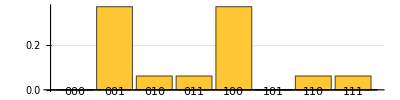

```mathematica
measurements["ProbabilitiesPlot",]
```

Notice that the possible outcomes of a quantum measurement are simply classical bit sequences. In the earlier classical computation examples, the rules were deterministic: each input led to a definite output. In contrast, quantum computation typically yields a range of possible outcomes, each with a certain probability. This is because quantum theory provides a probabilistic description of measurement results, with the distribution determined by the state just before measurement (and the chosen measurement basis).

## How Quantum State Changes

Additionally, you can compute how the quantum state evolves as gates are applied. Although we have not yet discussed the state in full detail, for now focus on the linear combination of computational-basis bitstrings and examine the coefficient (amplitude) of each term. These amplitudes update linearly under gates, and their  squared magnitudes determine the probabilities of the corresponding bitstrings upon measurement.

```mathematica
Grid[Prepend[Transpose[{{"Initial","H","Z","Y","P[π/4]","CNOT","RY[π/3]","CH","Measurements"},TraditionalForm/@FoldList[#2[#1]&,QuantumState["000"],qc["Operators"]]}],Style[#,Bold]&/@{"Step","State"}],Frame->All,Alignment->Left]
```

Step | State
Initial | 000
H | 1/(√2)000+1/(√2)100
Z | 1/(√2)000+1/(√2)100
Y | ⅈ/(√2)001+ⅈ/(√2)101
P[π/4] | ⅈ/(√2)001+(ⅈ ⅇ^((ⅈ π)/4))/(√2)101
CNOT | ⅈ/(√2)001+(ⅈ ⅇ^((ⅈ π)/4))/(√2)100
RY[π/3] | 1/2 ⅈ √(3/2)001+ⅈ/(2 √2)011+1/2 ⅈ √(3/2) ⅇ^((ⅈ π)/4)100+(ⅈ ⅇ^((ⅈ π)/4))/(2 √2)110
CH | 1/2 ⅈ √(3/2)001+ⅈ/4 010-ⅈ/4011+1/2 ⅈ √(3/2) ⅇ^((ⅈ π)/4)100+1/4 ⅈ ⅇ^((ⅈ π)/4)110+1/4 ⅈ ⅇ^((ⅈ π)/4)111
Measurements | <|000→0,001→3/8,010→1/16,011→1/16,100→3/8,101→0,110→1/16,111→1/16|>

Keep in mind that, in the end, the most important information we extract from a quantum system is its measurement results (and their statistics). We will discuss this in more detail in future chapters.

## Summary

Quantum computation encodes information in qubits and applies quantum gates to transform quantum states toward a computational goal.

Quantum circuits are read left to right, with wires for qubits, boxes for gates, and measurement steps that output classical bit strings.

A multi-qubit system has a set of computational basis states that serve as the standard reference states for describing quantum data.

Quantum states can be superpositions, meaning they combine multiple basis states with complex-valued weights.

Simulators (like the Wolfram Quantum Framework) model quantum evolution and measurement on classical hardware, producing probabilistic outcomes but not quantum speedups.